```mathematica
(*Calcs for Lab*)
```

```mathematica
(*Michelson interferometer*)
```

```mathematica
(*Red Laser Light*)
```

```mathematica
RedReads= {0.07,0.10,0.13,0.17,0.20,0.23,0.26,0.30,0.33,0.36}-0.07(*10 fringes*);
RedFshift = 10*Range[0, Length[RedReads]-1];
```

```mathematica
RedData = Transpose[{RedFshift,RedReads, RedReads/10}];
RedHeader= {"Fringe Count", "Direct reading", "Actual Mirror shift(mm)"};
TableForm[RedData,TableHeadings->{None,RedHeader}]
```

Fringe Count | Direct reading | Actual Mirror shift(mm)
0 | 0. | 0.
10 | 0.03 | 0.003
20 | 0.06 | 0.006
30 | 0.1 | 0.01
40 | 0.13 | 0.013
50 | 0.16 | 0.016
60 | 0.19 | 0.019
70 | 0.23 | 0.023
80 | 0.26 | 0.026
90 | 0.29 | 0.029

```mathematica
RedGraph = Transpose[{RedReads/10, RedFshift}];
RedFit = NonlinearModelFit[RedGraph, m*x, {{m, 3333.4}}, x];
RedFunction[x_] = Normal[RedFit];
```

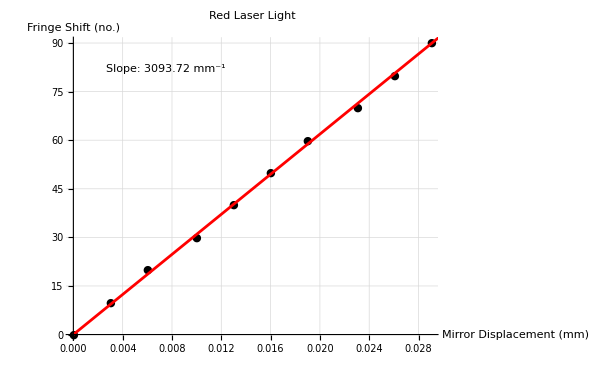

```mathematica
RedRawDataGraph = ListPlot[RedGraph, PlotMarkers -> "\\[FilledCircle]", GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed], PlotStyle -> {Black, PointSize[Medium]}, PlotLabel->"Red Laser Light", AxesLabel->{"Mirror Displacement (mm)", "Fringe Shift (no.)"}];
RedFitDataGraph = Plot[RedFunction[x], {x, 0, 0.03}, PlotStyle -> Red, PlotRange -> All];
Show[RedRawDataGraph,RedFitDataGraph, Epilog->{Text[StringForm["Slope: `1` mm^-1", RedFitSlope], {0.0075, 82}]},Background -> White, AxesStyle -> Black, PlotStyle -> Black]
```

```mathematica
RedFitSlope = m/.RedFit["BestFitParameters"];
Print[ "The best-fit value for the wavelength of red laser light, based on the measured data, is ", 2/RedFitSlope*10^6, " nm."]
```

The best-fit value for the wavelength of red laser light, based on the measured data, is 646.471 nm.

```mathematica
(*Blue Laser Light*) (*Edit: Should be violet, but accidentally mistook as blue*)
```

```mathematica
BlueReads = {0.87,0.89,0.91,0.93,0.96,0.97,1.0,1.01,1.03,1.05}-0.87 (*10 fringes*);
BlueFshift = 10*Range[0,Length[BlueReads]-1];
```

```mathematica
BlueData = Transpose[{BlueFshift,BlueReads, BlueReads/10}];
BlueHeader= {"Fringe Count", "Direct reading", "Actual Mirror shift(mm)"};
TableForm[BlueData,TableHeadings->{None,BlueHeader}]
```

Fringe Count | Direct reading | Actual Mirror shift(mm)
0 | 0. | 0.
10 | 0.02 | 0.002
20 | 0.04 | 0.004
30 | 0.06 | 0.006
40 | 0.09 | 0.009
50 | 0.1 | 0.01
60 | 0.13 | 0.013
70 | 0.14 | 0.014
80 | 0.16 | 0.016
90 | 0.18 | 0.018

```mathematica
BlueGraph = Transpose[{BlueReads/10, BlueFshift}];
BlueFit = NonlinearModelFit[BlueGraph, m*x, {{m, 4900}}, x];
BlueFunction[x_] = Normal[BlueFit];
```

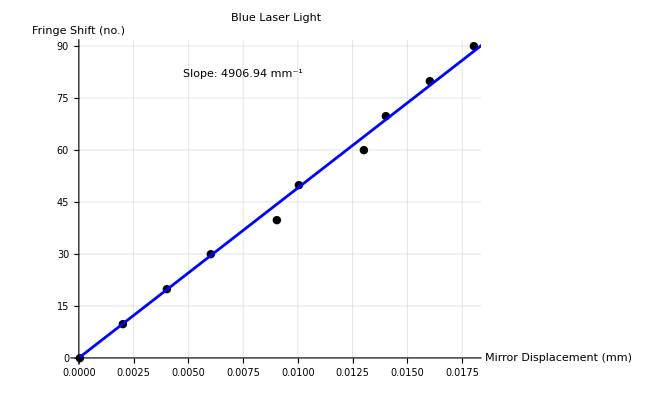

```mathematica
BlueRawDataGraph = ListPlot[BlueGraph, PlotMarkers -> "\\[FilledCircle]", GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed], PlotStyle -> {Black, PointSize[Medium]}, PlotLabel->"Blue Laser Light", AxesLabel->{"Mirror Displacement (mm)", "Fringe Shift (no.)"}];
BlueFitDataGraph = Plot[BlueFunction[x], {x, 0, 0.02}, PlotStyle -> Blue, PlotRange -> All];
Show[BlueRawDataGraph,BlueFitDataGraph,Epilog->{Text[StringForm["Slope: `1` mm^-1", BlueFitSlope], {0.0075, 82}]},Background -> White, AxesStyle -> Black, PlotStyle -> Black]
```

```mathematica
BlueFitSlope = m/.BlueFit["BestFitParameters"];
Print[ "The best-fit value for the wavelength of purple laser light, based on the measured data, is ", 2/BlueFitSlope*10^6, " nm."]
```

The best-fit value for the wavelength of purple laser light, based on the measured data, is 407.586 nm.

```mathematica
(*Green Laser Light*)
```

```mathematica
GreenReads = {0.0,0.09,0.16,0.25} (*30-31 fringes*);
GreenFshift = {0,30,61,92};
```

```mathematica
GreenData = Transpose[{GreenFshift,GreenReads, GreenReads/10}];
GreenHeader= {"Fringe Count", "Direct reading", "Actual Mirror shift(mm)"};
TableForm[GreenData,TableHeadings->{None,GreenHeader}]
```

Fringe Count | Direct reading | Actual Mirror shift(mm)
0 | 0. | 0.
30 | 0.09 | 0.009
61 | 0.16 | 0.016
92 | 0.25 | 0.025

```mathematica
GreenGraph = Transpose[{GreenReads/10, GreenFshift}];
GreenFit = NonlinearModelFit[GreenGraph, m*x, {{m, 3333.4}}, x];
GREENFunction[x_] = Normal[GreenFit];
```

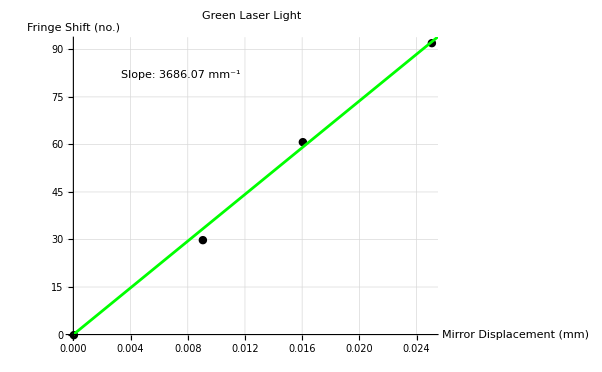

```mathematica
GreenRawDataGraph = ListPlot[GreenGraph, PlotMarkers -> "\\[FilledCircle]", GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed], PlotStyle -> {Black, PointSize[Medium]}, PlotLabel->"Green Laser Light", AxesLabel->{"Mirror Displacement (mm)", "Fringe Shift (no.)"}];
GreenFitDataGraph = Plot[GREENFunction[x], {x, 0, 0.03}, PlotStyle -> Green, PlotRange -> All];
Show[GreenRawDataGraph,GreenFitDataGraph,Epilog->{Text[StringForm["Slope: `1` mm^-1", GreenFitSlope], {0.0075, 82}]},Background -> White, AxesStyle -> Black, PlotStyle -> Black]
```

```mathematica
GreenFitSlope = m/.GreenFit["BestFitParameters"];
Print[ "The best-fit value for the wavelength of green laser light, based on the measured data, is ", 2/GreenFitSlope*10^6, " nm."]
```

The best-fit value for the wavelength of green laser light, based on the measured data, is 542.583 nm.